# Practical 1

HARIOM (20201022)

### Command used :

```mathematica
?Show
```

Show[graphics,options] shows graphics with the specified options added. 
Show[g_1,g_2,…] shows several graphics combined.

```mathematica
?ListPlot
```

ListPlot[{y_1,y_2,…}] plots points {1,y_1},{2,y_2},…. 
ListPlot[{{x_1,y_1},{x_2,y_2},…}] plots a list of points with specified x and y coordinates. 
ListPlot[{data_1,data_2,…}] plots data from all the data_i.
ListPlot[{…,w[data_i,…],…}] plots data_i with features defined by the symbolic wrapper w.

```mathematica
?Table
```

Table[expr,n] generates a list of n copies of expr. 
Table[expr,{i,i_max}] generates a list of the values of expr when i runs from 1 to i_max. 
Table[expr,{i,i_min,i_max}] starts with i=i_min. 
Table[expr,{i,i_min,i_max,di}] uses steps di. 
Table[expr,{i,{i_1,i_2,…}}] uses the successive values i_1, i_2, ….
Table[expr,{i,i_min,i_max},{j,j_min,j_max},…] gives a nested list. The list associated with i is outermost.

```mathematica
?AspectRatio
```

AspectRatio is an option for Graphics and related functions that specifies the ratio of height to width for a plot.

### Make a geometric plot to show that the nth roots of unity are equally spaced points that lie on the unit circle and form the vertices of a regular polygon with n sides , for n = 4, 5, 6, 7, 8

n=3

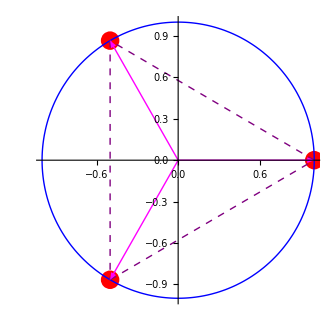

```mathematica
a:=ListPlot[Table[{Re[Exp[2*Pi*I*n/3]], Im[Exp[2*Pi*I*n/3]]},{n,0,2}],
AspectRatio-> Automatic,PlotStyle->{Red,PointSize[0.04]}];
b:=ParametricPlot[{Cos[t],Sin[t]},{t,0,2*Pi},PlotStyle->{Thick,Blue}];
c:=Table[Graphics[{Thick,Magenta,Arrow[{{0,0},{Re[Exp[2*Pi*I*n/3]],Im[Exp[2*Pi*I*n/3]]}}]}],{n,0,2}];
d:=Table[Graphics[{Thick,Dashed,Purple,Line[{{Re[Exp[2*Pi*I*n/3]],Im[Exp[2*Pi*I*n/3]]},{Re[Exp[2*Pi*I(n+1)/3]],Im[Exp[2*Pi*I*(n+1)/3]]}}]}],{n,0,2}];

Show[a,b,c,d,PlotRange->1.25]
```

Command a gives the points
command b gives the circle
command c gives the arrows
command d gives the dashed lines

Q2. Plotting 4^th roots of unity.

n=4

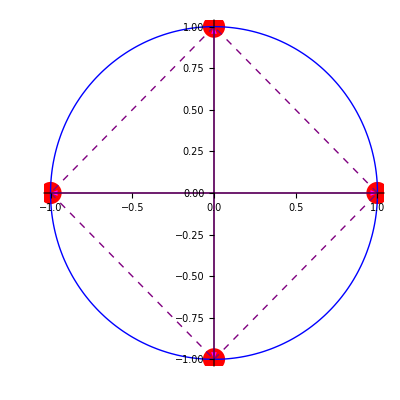

```mathematica
a:=ListPlot[Table[{Re[Exp[2*Pi*I*n/4]], Im[Exp[2*Pi*I*n/4]]},{n,0,3}],
AspectRatio-> Automatic,PlotStyle->{Red,PointSize[0.04]}];
b:=ParametricPlot[{Cos[t],Sin[t]},{t,0,2*Pi},PlotStyle->{Thick,Blue}];
c:=Table[Graphics[{Thick,Magenta,Arrow[{{0,0},{Re[Exp[2*Pi*I*n/4]],Im[Exp[2*Pi*I*n/4]]}}]}],{n,0,3}];
d:=Table[Graphics[{Thick,Dashed,Purple,Line[{{Re[Exp[2*Pi*I*n/4]],Im[Exp[2*Pi*I*n/4]]},{Re[Exp[2*Pi*I(n+1)/4]],Im[Exp[2*Pi*I*(n+1)/4]]}}]}],{n,0,3}];

Show[a,b,c,d,PlotRange->1.25]
```

Q3. Plotting 5^th roots of unity.

n=5

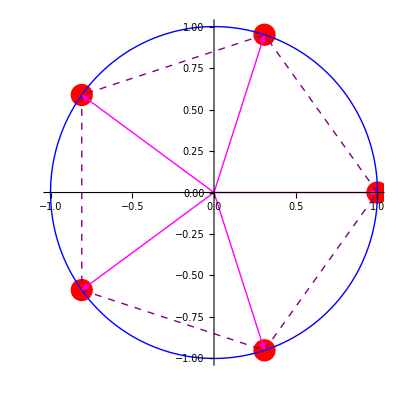

```mathematica
a:=ListPlot[Table[{Re[Exp[2*Pi*I*n/5]], Im[Exp[2*Pi*I*n/5]]},{n,0,4}],
AspectRatio-> Automatic,PlotStyle->{Red,PointSize[0.04]}];
b:=ParametricPlot[{Cos[t],Sin[t]},{t,0,2*Pi},PlotStyle->{Thick,Blue}];
c:=Table[Graphics[{Thick,Magenta,Arrow[{{0,0},{Re[Exp[2*Pi*I*n/5]],Im[Exp[2*Pi*I*n/5]]}}]}],{n,0,4}];
d:=Table[Graphics[{Thick,Dashed,Purple,Line[{{Re[Exp[2*Pi*I*n/5]],Im[Exp[2*Pi*I*n/5]]},{Re[Exp[2*Pi*I(n+1)/5]],Im[Exp[2*Pi*I*(n+1)/5]]}}]}],{n,0,4}];

Show[a,b,c,d,PlotRange->1.25]
```

Q4. Plotting 6^th roots of unity.

n=6

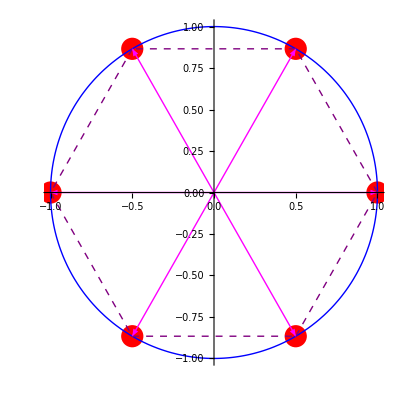

```mathematica
a:=ListPlot[Table[{Re[Exp[2*Pi*I*n/6]], Im[Exp[2*Pi*I*n/6]]},{n,0,5}],
AspectRatio-> Automatic,PlotStyle->{Red,PointSize[0.04]}];
b:=ParametricPlot[{Cos[t],Sin[t]},{t,0,2*Pi},PlotStyle->{Thick,Blue}];
c:=Table[Graphics[{Thick,Magenta,Arrow[{{0,0},{Re[Exp[2*Pi*I*n/6]],Im[Exp[2*Pi*I*n/6]]}}]}],{n,0,5}];
d:=Table[Graphics[{Thick,Dashed,Purple,Line[{{Re[Exp[2*Pi*I*n/6]],Im[Exp[2*Pi*I*n/6]]},{Re[Exp[2*Pi*I(n+1)/6]],Im[Exp[2*Pi*I*(n+1)/6]]}}]}],{n,0,5}];

Show[a,b,c,d,PlotRange->1.25]
```

Q5. Plotting 7^th roots of unity.

n=7

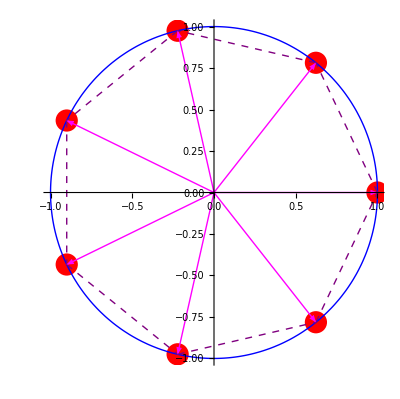

```mathematica
a:=ListPlot[Table[{Re[Exp[2*Pi*I*n/7]], Im[Exp[2*Pi*I*n/7]]},{n,0,6}],
AspectRatio-> Automatic,PlotStyle->{Red,PointSize[0.04]}];
b:=ParametricPlot[{Cos[t],Sin[t]},{t,0,2*Pi},PlotStyle->{Thick,Blue}];
c:=Table[Graphics[{Thick,Magenta,Arrow[{{0,0},{Re[Exp[2*Pi*I*n/7]],Im[Exp[2*Pi*I*n/7]]}}]}],{n,0,6}];
d:=Table[Graphics[{Thick,Dashed,Purple,Line[{{Re[Exp[2*Pi*I*n/7]],Im[Exp[2*Pi*I*n/7]]},{Re[Exp[2*Pi*I(n+1)/7]],Im[Exp[2*Pi*I*(n+1)/7]]}}]}],{n,0,6}];

Show[a,b,c,d,PlotRange->1.25]
```

Q6. Plotting 8^th roots of unity.

n=8

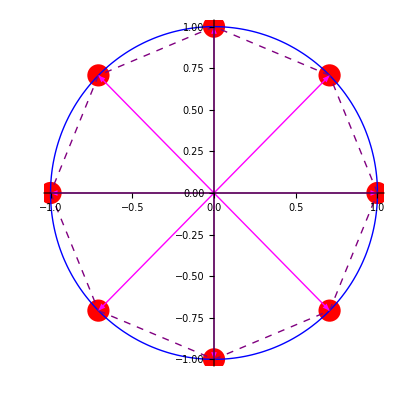

```mathematica
a:=ListPlot[Table[{Re[Exp[2*Pi*I*n/8]], Im[Exp[2*Pi*I*n/8]]},{n,0,7}],
AspectRatio-> Automatic,PlotStyle->{Red,PointSize[0.04]}];
b:=ParametricPlot[{Cos[t],Sin[t]},{t,0,2*Pi},PlotStyle->{Thick,Blue}];
c:=Table[Graphics[{Thick,Magenta,Arrow[{{0,0},{Re[Exp[2*Pi*I*n/8]],Im[Exp[2*Pi*I*n/8]]}}]}],{n,0,7}];
d:=Table[Graphics[{Thick,Dashed,Purple,Line[{{Re[Exp[2*Pi*I*n/8]],Im[Exp[2*Pi*I*n/8]]},{Re[Exp[2*Pi*I(n+1)/8]],Im[Exp[2*Pi*I*(n+1)/8]]}}]}],{n,0,7}];

Show[a,b,c,d,PlotRange->1.25]
```